```mathematica
ClearAll["Global`*"];
```

```mathematica
SetOptions[Plot3D,ImageSize->800]; SetOptions[Plot,ImageSize->800];
SetOptions[ContourPlot,ImageSize->800]; SetOptions[ListPlot,ImageSize->800];
SetOptions[ParametricPlot,ImageSize->800];
```

```mathematica
ω = 0.0228;
ℰ = 0.0655;
Ip = 0.579;
```

```mathematica
t1 = 2π/ω;(* == 0 *)
t2 = 3.5π/ω;(* == π/(2ω) *)
px0 =(ℰ/ω)(ω t0-π/2);
py0 = v0;
px1 = π ℰ/ (2Ip)^(3/2);
py1 = - 2 v0 ℰ / (2Ip)^2;
px2 = 0;
px1t1 = px0+px1 + ℰ/ω; 
y1t1 = (py0+py1)(t1-t0);
py2 = -2/(px1t1 y1t1);
x2t2 = -2ℰ/ω^2 + (px0+px1)(t2-t0) -Ip/ℰ;
y2t2 = (py0+py1)(t1-t0) +(py0+py1+py2)(t2-t1);
r2t2 = √(x2t2^2+y2t2^2);

ξ =x2t2/r2t2;
JJX[ξ_] = 0.847213+0.927037ξ-0.317705 ξ^2(*+0.193132 ξ^3*);
JJY[ξ_] = 1.854074-1.270819 ξ+1.158796 ξ^2(1+ξ)^-1;
px3 = -√(2/ℰ)1/r2t2^(3/2) JJX[ξ];
py3 = -√(2/ℰ)y2t2/r2t2^(5/2) JJY[ξ];

px = px0 + px1 + px2  + px3;
py = py0 + py1 + py2  + py3;

(*{px,py}*)
fpx[v0_,t0_] = Evaluate[px];
fpy[v0_,t0_] = Evaluate[py];
fmomentum[v0_,t0d_] = {fpx[v0,2π t0d/(360ω)],fpy[v0,2π t0d/(360ω)]};
jac[v0_,t0_] =  D[fpx[v0,t0],t0]*D[fpy[v0,t0],v0] - D[fpx[v0,t0],v0]*D[fpy[v0,t0],t0];
jacd[v0_,t0d_] =jac[v0, 2π t0d/(360ω)];
```

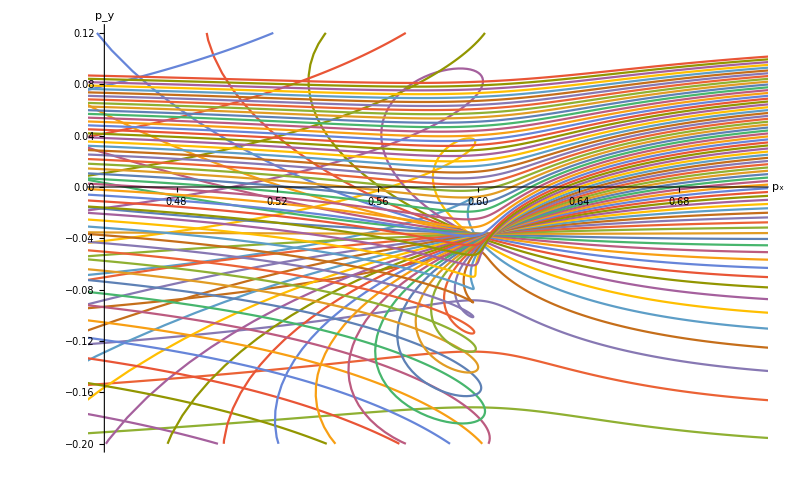

```mathematica
p1 = ListPlot[
ParallelTable[
fmomentum[v0,t0d],
{v0,0.01,0.15, 0.002},
{t0d,95,105,0.03}
],
PlotRange->{{0.45,0.71},{-0.2,0.12}},
Joined->True,
AxesLabel-> {"p_x","p_y"},
AxesStyle->Directive[Black,FontSize->14]
]
```

```mathematica
jplot = ContourPlot[
jac[v0,2π t0d/(360ω)],
{t0d,95,105},
{v0,0.01,0.15},
MaxRecursion->4,
Contours -> {0}
];
```

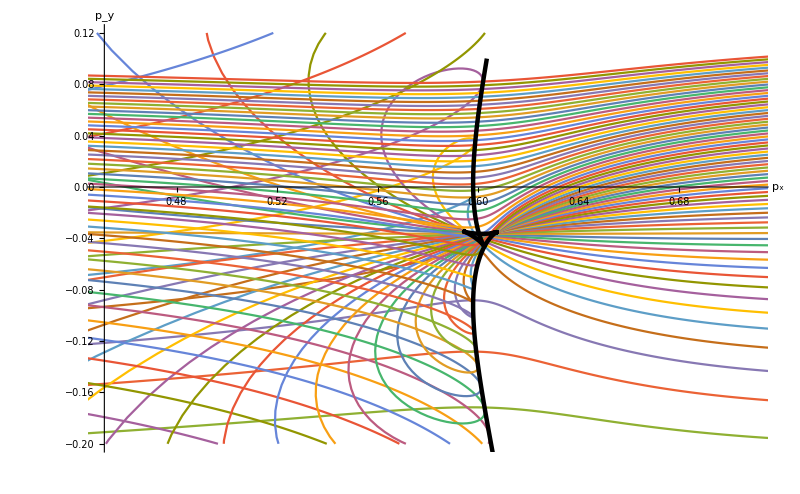

```mathematica
zeroline =  Cases[Normal@jplot,Line[pts_,___]:>pts,Infinity][[1]];
zerolinePxPy =(fmomentum[#[[2]],#[[1]]])&/@ zeroline;
p2 = ListPlot[
zerolinePxPy,
PlotRange->{{0.2,0.7},{-0.22,0.1}},
Joined->True,
PlotStyle->{Black,Thickness[0.004]},
AxesLabel-> {"p_x, a.u.", "p_y, a.u."},
AxesStyle->Directive[Black,FontSize->14],
AspectRatio -> 1.8
];
Show[p1,p2(*,Graphics[Inset[Style["×",25]*)(*,JZeros*)]
```